```mathematica
Remove["Global`*"];
```

```mathematica
tmax=40;
ω=1;g=10;l=1;h=40;
L=Piecewise[{{1/2(y1'[t]^2+y2'[t]^2)-1/(y2[t]-y1[t])^4,y2[t]-y1[t]<0.1},{1/2(y1'[t]^2+y2'[t]^2)-1/y1[t]^4,y1[t]<0.1},{1/2(y1'[t]^2+y2'[t]^2)-1/y2[t]^4,y2[t]<0.1}},1/2(y1'[t]^2+y2'[t]^2)- g(y1[t]+y2[t])-1/2 ω^2(y2[t]-y1[t]-l)^2];
eom={D[L,y1[t]]==Dt[D[L,y1'[t]],t],D[L,y2[t]]==Dt[D[L,y2'[t]],t]};
```

```mathematica
soln=NDSolveValue[Join[eom,{y1[0]==h,y2[0]==l+h+g/ω^2,y1'[0]==0,y2'[0]==0}],{y1[t],y2[t]},{t,0,tmax}];
```

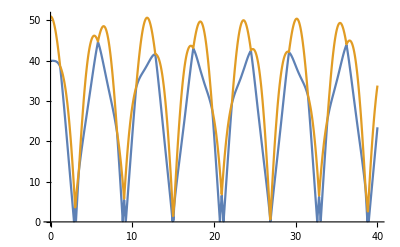

```mathematica
Plot[soln,{t,0,tmax}]
```

```mathematica
sy1[i_]:=soln[[1]]/.t->i;sy2[i_]:=soln[[2]]/.t->i;
```

```mathematica
Animate[
Graphics[
{
PointSize[Large],
Red,Point[{0,sy1[t]}],
Blue,Point[{0,sy2[t]}],
Black,Line[{{-1, 0}, {1,0}}]
},
PlotRange->{{-1,1},{0,55}}
],
{t,0,tmax},AnimationRate->1]
```